```mathematica
Decomposicao de um tensor
```

de Decomposicao tensor um

```mathematica
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]]
(*ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
sigvec={sig1,sig2,sig3}
sigstar1=ROT.sigvec
I1=Tr[sigvec IdentityMatrix[3]];
J2=j2[sigvec IdentityMatrix[3]]
J3=Det[s[sigvec IdentityMatrix[3]]];
Xi=I1/Sqrt[3]
Rho=Sqrt[2J2]
BetA=(1/3) ArcCos[(3 √3)/2 J3/J2^(3/2)]//Simplify*)
```

```mathematica
(*sigma={{sigr,0,0},{0,sigr,0},{0,0,sigax}}
j2[sigma]//Simplify*)
```

```mathematica
(*Simplify[sigstar1[[1]]-Xi]
Simplify[Sqrt[((sigstar1[[2]]^2+sigstar1[[3]]^2))]-Rho]
Simplify[ArcTan[sigstar1[[3]]/sigstar1[[2]]]-BetA]/.{sig1 ->3,sig2->2,sig3->1}
sub={ξ->(sig1+sig2+sig3)/Sqrt[3],ρ->Sqrt[2J2] ,β->ArcTan[(√3 (-sig2+sig3))/(-2 sig1+sig2+sig3)]};
TT=({{1, 0, 0}, {0, Cos[β], 0}, {0, 0, ρ Sin[β]/β}});
R=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
veccyl={ξ,ρ,β};
vecrinc={sig1,sig2,sig3};
Simplify[(TT.veccyl/.sub)-(R.vecrinc)]/.{sig1->3,sig2->2,sig3->1}*)
```

```mathematica
Young=100;
Poisson=0.25;
lambda=(Poisson*Young)/((1+Poisson)*(1-2 Poisson));
mu=Young/(2(1+Poisson));
(*G=(Young)/(2*(1+Poisson));*)
Kk=(Young)/(3*(1-2Poisson));
Sigma[Eelastico_]:=lambda Tr[Eelastico]IdentityMatrix[3]+2 mu Eelastico;
ComputeStrain[sigma_]:=1/(9K)Tr[sigma]IdentityMatrix[3]+1/(2G)s[sigma];
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
i1[sigma_]:=Tr[sigma]; 
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]];
subst = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424,ψ->1,NN->0,G->40}
Spectrum[sigma_]:=Block[{i,xy,xz,yz,val2,J3,J2,x1a,x2a,x3a,theta,eigenval,eigenvec,I1,I3,I2,e1,e2,e3,S,temp,j,Q,R,x1,x2,x3,val,X,eigensis,a,b,c,size},
size=Length[sigma];
eigenval=Eigenvalues[sigma];
eigenvec=Eigenvectors[sigma];
eigensis=Eigensystem[sigma];
(*Print["sigma = ",sigma];
Print["eigenval = ",eigenval];
Print["eigenvec = ",eigenvec];*)
I1=Tr[sigma]; 
I2=1/2(Tr[sigma]^2-Tr[sigma.sigma]); 
I3=Det[sigma];

(*Print["I1 = ",I1];
Print["I2 = ",I2];
Print["I3 = ",I3];*)
R=(-2 I1^3+9I1 I2-27 I3)/54.;
(*Print["R = ",R];*)
Q=(I1^2-3 I2)/9.;

If[Q<1*10^-15,Q=1*10^-15];
val=R/(√(Q^3));

If[Abs[val]<1,
theta=ArcCos[val];
];

If[val≥ 1,
theta=0;
];
If[val≤ - 1,
theta=Pi;
];

x1=-2 √Q Cos[theta/3]+I1/3;
x2=-2 √Q Cos[(theta+2Pi)/3]+I1/3;
x3=-2 √Q Cos[(theta-2Pi)/3]+I1/3;

If[x1< x2,temp=x1; x1=x2;x2=temp;];
If[x2< x3,temp=x2; x2=x3;x3=temp;];
If[(x2-x3<1*10^-5)&& (x1-x2≥ 10^-5) , 

(*Print["x1≠ x2 && x2==x3"];*)

e1=(x1/(2 x1^3-I1 x1^2+I3)(sigma.sigma-(I1-x1)sigma+I3/x1 IdentityMatrix[size]));
e2=IdentityMatrix[size]-e1;
e3=IdentityMatrix[size] 0;


(*Print["e1 = ",e1//MatrixForm];
Print["e2 = ",e2//MatrixForm];
Print["e3 = ",e3//MatrixForm];*)

Return[{x1,x2,x3,e1,e2,e3}];

,If[(x1-x2)<10^-5 && (x2-x3)≥ 10^-5,
(*Print["x1= x2 && x2!=x3"];*)
e3=x3/(2 x3^3-I1 x3^2+I3)(sigma.sigma-(I1-x3)sigma+I3/x3 IdentityMatrix[size]);

e2=IdentityMatrix[size]-e3;
e1=IdentityMatrix[size] 0;


Return[{x1,x2,x3,e1,e2,e3}];

,If[x1-x2<1*10^-5&& x2-x3<1*10^-5,

(*Print[" x1 == x2 && x2 == x3"];*)

e1=IdentityMatrix[size] ;
e2=IdentityMatrix[size] 0;
e3=IdentityMatrix[size] 0;
Return[{x1,x2,x3,e1,e2,e3}];

,

(*If[x1≠ x2 && x2≠ x3 ,*)

(*Print[" x1 != x2 && x2 != x3"];*)

e1=x1/(2 x1^3-I1 x1^2+I3)(sigma.sigma-(I1-x1)sigma+I3/x1 IdentityMatrix[3]);
e2=x2/(2 x2^3-I1 x2^2+I3)(sigma.sigma-(I1-x2)sigma+I3/x2 IdentityMatrix[3]);
e3=x3/(2 x3^3-I1 x3^2+I3)(sigma.sigma-(I1-x3)sigma+I3/x3 IdentityMatrix[3]);
Return[{x1,x2,x3,e1,e2,e3}]

(*];*)
]
]
]

];
```

{A→152.54,B→0.0015489,C→146.29,D→0.018768,W→0.006605,R→0.91969,K→16424,ψ→1,NN→0,G→40}

```mathematica
flag=True;
flag2=True;(*If True bate com philippe e ψ deve ser = 1 para bater*)

Γ[β_]:=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
(*SinPhi[ψ_]:=(3(1-ψ))/(1+ψ)
Γ[β_]:=(2Sqrt[3])/(3-SinPhi[ψ])(Cos[β]-(SinPhi[ψ]Sin[β])/Sqrt[3]);*)
FF[x_,ϕ_]:=(A-C Exp[x B]-ϕ x);
EpsEqX[X_]:=W E^(D X)(*phil mexeu *)
XEqL[L_]:=L-R FF[L,ϕ]
EpsEqL[L_]:=EpsEqX[XEqL[L]]
s[sigma_]:=sigma-1/3 Tr[sigma]IdentityMatrix[3];
T[ξ_,ρ_,β_]:=Block[{sig1,sig2,sig3},
sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Cos[β];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Cos[β-2Pi/3];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Cos[β+2Pi/3];

(*sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Sin[β-2Pi/3];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Sin[β];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Sin[β+2Pi/3];*)

Return[{sig1,sig2,sig3}];
]
(* Ponto de F1 no espaco Haigh Westergaard coordenadas cylindricas *)
F1HWCyl[ξ_,β_]:=Block[{A,B,C,W,ψ,NN,ϕ,I1,sqrtj2,ρ,sig1,sig2,sig3},

FF[I1_,ϕ_]:=A-C Exp[I1 B]-ϕ I1;
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ[β];
ρ=Sqrt[2]sqrtj2;
Return[{ξ,ρ,β}];
]
(* Ponto de F1 no espaco Haigh Westergaard *)
(* Diogo - nao tenho certeza que eh cos[beta] sin[beta] *)
F1HWCart[ξ_,β_]:=Block[{temp},
temp=F1HWCyl[ξ,β];
{temp[[1]],Cos[temp[[3]]]temp[[2]],Sin[temp[[3]]]temp[[2]]}
]
(* Ponto de F1 no espaco de tensoes principais *)
F1[ξ_,β_]:=Block[{FHW},
FHW=F1HWCyl[ξ,β];
Return[T[FHW[[1]],FHW[[2]],FHW[[3]]]];
]
F2HWCyl[θ_,β_,L_]:=Block[{R,A,B,C,W,ψ,NN,ϕ,I1,sqrtj2,ρ,sig1,sig2,sig3,ξ},
I1=L+R FF[L,ϕ]Cos[θ];
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ[β];
ξ=I1/Sqrt[3];
ρ=sqrtj2 Sqrt[2];
Return[{ξ,ρ,β}];
]
F2HWCart[θ_,β_,L_]:=Block[{temp},
temp=F2HWCyl[θ,β,L];
{temp[[1]],Cos[temp[[3]]]temp[[2]],Sin[temp[[3]]]temp[[2]]}
]
F2[θ_,β_,L_]:=Block[{FHW},
FHW=F2HWCyl[θ,β,L];
Return[T[FHW[[1]],FHW[[2]],FHW[[3]]]];
]

DistFunc1[pt_,ξ_,β_]:=Block[{parametrictrial,parametric,x,p1,y,p2,z,p3,distf1,sig,sigtrial,sigHW,sig2,sig3,sig1tr,sig2tr,sig3tr,haigh,haightrial,G,K,Rot},
Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
(*parametriza os pontos das coordenadas {ξ,ρ,β} para {ξ,θ,β}*)
parametric=F1HWCart[ξ,β];
(*Matriz de rotacao que parametriza os pontos das coordenadas {σ1,σ2,σ3} para {ξ,θ,β}*)
parametrictrial=Rot.pt;


distf1=Sqrt[1/(3 K)(parametrictrial[[1]]-parametric[[1]])^2 +1/(2G)((parametrictrial[[2]]-parametric[[2]])^2 +(parametrictrial[[3]]-parametric[[3]])^2)];
Return[distf1]
];
DistFunc2[pt_,θ_,β_,L_]:=Block[{parametrictrial,parametric,distf2,haigh,haightrial,G,K,Rot},

Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
(*parametriza os pontos das coordenadas {ξ,ρ,β} para {ξ,θ,β}*)
parametric=F2HWCart[θ,β,L];
(*Matriz de rotacao que parametriza os pontos das coordenadas {σ1,σ2,σ3} para {ξ,θ,β}*)
parametrictrial=Rot.pt;
distf2=Sqrt[1/(3 K)(parametrictrial[[1]]-parametric[[1]])^2 +1/(2G)((parametrictrial[[2]]-parametric[[2]])^2 +(parametrictrial[[3]]-parametric[[3]])^2)];
Return[distf2]
];
```

```mathematica
F1HWCart[ξ,β]
```

{ξ,(2 √2 (A-C ⅇ^(√3 B ξ)-NN-√3 ξ ϕ) Cos[β])/(1+(1-Sin[3 β])/ψ+Sin[3 β]),(2 √2 (A-C ⅇ^(√3 B ξ)-NN-√3 ξ ϕ) Sin[β])/(1+(1-Sin[3 β])/ψ+Sin[3 β])}

```mathematica
F1HWCyl[ξ,β]
```

{ξ,(2 √2 (A-C ⅇ^(√3 B ξ)-NN-√3 ξ ϕ))/(1+(1-Sin[3 β])/ψ+Sin[3 β]),β}

```mathematica
Funcoes de Sandler Dimaggio PV
```

de Dimaggio Funcoes PV Sandler

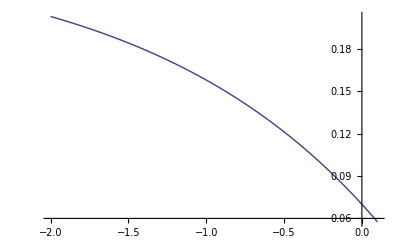

```mathematica
Plot[FF[I1,0]/.subst,{I1,-2,0.1}]
```

```mathematica
Transformacoes
```

Transformacoes

```mathematica
J2=j2[{sig1,sig2,sig3}IdentityMatrix[3]]
```

1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)

```mathematica
FromHWCylToHWCart[vec_]:=Block[{sig2tiu,sig3tiu,ξ,ρ,β},
ξ=vec[[1]];
ρ=vec[[2]];
β=vec[[3]];
sig2tiu=ρ Cos[β];
sig3tiu=ρ Sin[β];
{ξ,sig2tiu,sig3tiu}
];
FromHWCartToHWCyl[vec_]:=Block[{ρ,β,ξ,sig2tiu,sig3tiu},
ξ=vec[[1]];
sig2tiu=vec[[2]];
sig3tiu=vec[[3]];
ρ=Sqrt[sig2tiu^2+sig3tiu^2];
β=ArcTan[sig2tiu,sig3tiu];
{ξ,ρ,β}
];
FromHWCylToPrincipal[vec_]:=Block[{sig1,sig2,sig3,ξ,ρ,β},
ξ=vec[[1]];
ρ=vec[[2]];
β=vec[[3]];
sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Cos[β];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Cos[β-2Pi/3];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Cos[β+2Pi/3];
{sig1,sig2,sig3}
];
FromPrincipalToHWCyl[vec_]:=Block[{ROT,ξ,ρ,β,sig2tiu,sig3tiu,inter},
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
inter=(ROT.vec);
ξ=inter[[1]];
sig2tiu=inter[[2]];
sig3tiu=inter[[3]];

ρ=Sqrt[sig2tiu^2+sig3tiu^2];
β=ArcTan[sig2tiu,sig3tiu];
{ξ,ρ,β}
];
FromPrincipalToHWCart[vec_]:=Block[{ROT,ξ,ρ,β,sig2tiu,sig3tiu,inter},
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
inter=(ROT.vec);
ξ=inter[[1]];
sig2tiu=inter[[2]];
sig3tiu=inter[[3]];
{ξ,sig2tiu,sig3tiu}
];
FromPrincipalParametrized[vec_]:=Block[{ROT,ξ,ρ,β,sig1tiu,sig2tiu,sig3tiu,inter},
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
inter=(ROT.vec);
sig1tiu=inter[[1]];
sig2tiu=inter[[2]];
sig3tiu=inter[[3]];
{ArcTan[sig3tiu/sig1tiu],Sqrt[sig2tiu^2+sig3tiu^2],ArcTan[sig2tiu/sig3tiu]}
];
```

```mathematica
FromPrincipalParametrized[{sig1,sig2,sig3}]/.{sig1->3.,sig2->2,sig3->1}
```

{0.201358,1.41421,1.0472}

```mathematica
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
sigvec={sig1,sig2,sig3}
I1=Tr[sigvec IdentityMatrix[3]];
J2=j2[sigvec IdentityMatrix[3]]
J3=Det[s[sigvec IdentityMatrix[3]]];
Xi=I1/Sqrt[3]
Rho=Sqrt[2J2]
BetA=(1/3) ArcCos[(3 √3)/2 J3/J2^(3/2)]//Simplify
sig1star=Xi;
sig2star=Cos[BetA]Sqrt[2J2];
sig3star=Sin[BetA]Sqrt[2 J2];
theta=ArcTan[sig3star/sig1star]/.{sig1->3.,sig2->2,sig3->1}
rho=Sqrt[sig2star^2 +sig3star^2]/.{sig1->3.,sig2->2,sig3->1}
beta=ArcTan[sig2star/sig3star]/.{sig1->3.,sig2->2,sig3->1}
```

{sig1,sig2,sig3}

1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)

(sig1+sig2+sig3)/(√3)

√((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)

1/3 ArcCos[(2 sig1^3+2 sig2^3-3 sig2^2 sig3-3 sig2 sig3^2+2 sig3^3-3 sig1^2 (sig2+sig3)-3 sig1 (sig2^2-4 sig2 sig3+sig3^2))/(2 (sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3))^(3/2))]

0.201358

1.41421

1.0472

```mathematica
Derivadas
```

Derivadas

```mathematica
EpsEqX[X_]:=W E^(D X)(*phil mexeu *)
XEqL[L_]:=L-R FF[L,ϕ]
EpsEqL[L_]:=EpsEqX[XEqL[L]]
ResL[pt_,θ_,β_,L_,Lprev_]:=Block[{resl,haigh,haightrial,G,K,Rot,depspdl,A,R,B,W,d,I1,I1tr,ϕ,δL,l,L0,delepsp},

I1tr=pt[[1]]+pt[[2]]+pt[[3]];
I1=R FF[L,ϕ]Cos[θ]+L;
delepsp=EpsEqL[L]-EpsEqL[Lprev];
resl=3K delepsp- (I1tr-I1);
Return[resl]
];
DDistFunc1[pt_,ξ_,β_]:=Block[{a,b,res},
res={D[DistFunc1[pt,a,b]^2,a],D[DistFunc1[pt,a,b]^2,b]}/.{a->ξ,b->β};
res
]
D2DistFunc1[pt_,ξ_,β_]:=Block[{res,a,b},
res={{D[DistFunc1[pt,a,b]^2,a,a],D[DistFunc1[pt,a,b]^2,a,b]},
{D[DistFunc1[pt,a,b]^2,b,a],D[DistFunc1[pt,a,b]^2,b,b]}}/.{a->ξ,b->β};
res
]
DDistFunc2[pt_,θ_,β_,L_,Lprev_]:=Block[{a,b,c,res},
res={D[DistFunc2[pt,a,b,c]^2,a],D[DistFunc2[pt,a,b,c]^2,b],ResL[pt,a,b,c,Lprev]}/.{a->θ,b->β,c->L};
res
]
D2DistFunc2[pt_,θ_,β_,L_,Lprev_]:=Block[{res,a,b,c},
res={{D[DistFunc2[pt,a,b,c]^2,a,a],D[DistFunc2[pt,a,b,c]^2,a,b],D[DistFunc2[pt,a,b,c]^2,a,c]},
{D[DistFunc2[pt,a,b,c]^2,b,a],D[DistFunc2[pt,a,b,c]^2,b,b],D[DistFunc2[pt,a,b,c]^2,b,c]},
{D[ResL[pt,a,b,c,Lprev],a],D[ResL[pt,a,b,c,Lprev],b],D[ResL[pt,a,b,c,Lprev],c]}}/.{a->θ,b->β,c->L};
res
]
```

```mathematica
Algoritimos de projecao
```

Algoritimos de projecao

{0.116452,2.89903}

3 D ⅇ^(D (L-R (A-C ⅇ^(B L)-L ϕ))) K W (1-R (-B C ⅇ^(B L)-ϕ))

0.1+200. (-0.0658213+0.066 ⅇ^(0.67 (-2.5 (0.25-0.18 ⅇ^(0.67 L))+L)))

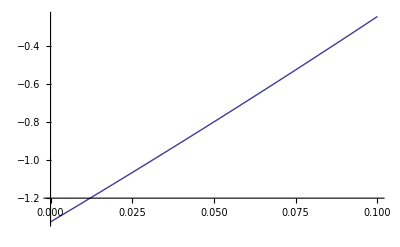

8.844 ⅇ^(0.67 (-2.5 (0.25-0.18 ⅇ^(0.67 L))+L)) (1+0.3015 ⅇ^(0.67 L))

```mathematica
MinF1[pt_]:=Block[{ϕ,distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,ξ,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,i,j,res,jac,resn,resn1,resnorm,counter,
chute,temp,I1,sol,f1,ptmin,xiguess,beta,distxi,distnew,betaguess},
resvec1={};
res=DDistFunc1[pt,ξ,β];
jac=D2DistFunc1[pt,ξ,β];
distxi=10^8;
βn=Pi;
For[xiguess=-Pi,xiguess≤Pi,xiguess+=Pi/20,
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc1[pt,xiguess,betaguess]/.subst;
If[Abs[distnew]<Abs[distxi],
ξn=xiguess;
βn=betaguess;
distxi=distnew;
];
];
];

resnorm=1;
counter=1;
resvec1={};
While[(resnorm>10^-12&&counter<30),
{ξn1,βn1}={ξn,βn}-Inverse[jac/.{ξ->ξn,β->βn}/.subst].(res/.{ξ->ξn,β->βn}/.subst);
resnorm=Norm[{ξn1,βn1}-{ξn,βn}];
(*Print["resnorm = ",resnorm];*)
AppendTo[resvec1,resnorm];
{ξn,βn}={ξn1,βn1};
counter++;
];
(*Print["resnorm = ",resnorm];*)
Return[{ξn,βn}]
];
MinF2[pt_,Lprev_]:=Block[{distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,θ,L,θn,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,
i,j,res,jac,resn,resn1,resnorm,counter,Ln,chute,θn1,temp,L0,Ln1,deltal,thetaguess,distnew,disttheta,betaguess},
res=DDistFunc2[pt,θ,β,L,Lprev];
jac=D2DistFunc2[pt,θ,β,L,Lprev];

disttheta=10^8;
βn=Pi;
For[thetaguess=0,thetaguess≤Pi,thetaguess+=Pi/20,
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc2[pt,thetaguess,betaguess,Lprev]/.subst;
If[Abs[distnew]<Abs[disttheta],
θn=thetaguess;
βn=betaguess;
disttheta=distnew;

];
];
];


Ln=Lprev;
resnorm=1;
counter=1;
resvec2={};
invjac=Inverse[jac/.{θ->θn,β->βn,L->Ln}/.subst];
deltal=0;
While[(resnorm>10^-15&&counter<30),
(*Print["iter = ",counter];
Print["θn = ",θn//N];
Print["βn= ",βn//N];
Print["Ln= ",Ln//N];
Print["JAC = ",jac/.{θ->θn,β->βn,L->Ln}/.subst//MatrixForm];
Print["res =  ",res/.{θ->θn,β->βn,L->Ln}/.subst//MatrixForm];*)
{θn1,βn1,Ln1}={θn,βn,Ln}-Inverse[jac/.{θ->θn,β->βn,L->Ln}/.subst].(res/.{θ->θn,β->βn,L->Ln}/.subst);

(*{θn1,βn1,Ln1}={θn,βn,Ln}-invjac.(res/.{θ->θn,β->βn,L->Ln}/.subst);*)
resnorm=Norm[{θn1,βn1,Ln1}-{θn,βn,Ln}];
(*Print["resnorm = ",resnorm];*)
{θn,βn,Ln}={θn1,βn1,Ln1};
AppendTo[resvec2,resnorm];
counter++;
];

Return[{θn,βn,Ln1-Lprev}]
];
MinF2θconst[pt_,Lprev_]:=Block[{distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,θ,θn,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,L,
i,j,res,jac,resn,resn1,resnorm,counter,Ln,chute,θn1,temp,L0,Ln1,deltal,θtr,thetaguess,betaguess,distnew,disttheta,θtr1},
res=DDistFunc2[pt,θ,β,L,Lprev];
jac=D2DistFunc2[pt,θ,β,L,Lprev];
βn=Pi;
θtr1=Pi/2;
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc2[pt,Pi/2,betaguess,Lprev]/.subst;
If[Abs[distnew]<Abs[disttheta],
βn=betaguess;
disttheta=distnew;
];
];
θtr=θtr1;
resnorm=1;
counter=1;
resvec2={};
Ln=Lprev;
invjac=Inverse[jac/.{θ->θtr1,β->βn,L->Lprev}/.subst];
deltal=0;
While[(resnorm>10^-15&&counter<30),
{θtr1,βn1,Ln1}={θtr,βn,Ln}-Inverse[jac/.{θ->θtr,β->βn,L->Ln}/.subst].(res/.{θ->θtr,β->βn,L->Ln}/.subst);
(*{θn1,βn1,Ln1}={θn,βn,Ln}-invjac.(res/.{θ->θn,β->βn,L->Ln}/.subst);*)
resnorm=Norm[{θtr1,βn1,Ln1}-{θtr1,βn,Ln}];
Print["resnorm = ",resnorm];
{θtr,βn,Ln}={θtr1,βn1,Ln1};
AppendTo[resvec2,resnorm];
counter++;
];

Return[{θtr,βn,Ln1-Lprev/.subst}]
];
pt={0.01,0.13,0.1};
MinF1[pt]
ResL2[pt_,L0_,I1pr_,I1tr_]:=Block[{resl,haigh,haightrial,G,K,Rot,depspdl,A,R,B,W,d,I1,ϕ,δL,l,L},

delepsp=EpsEqL[L]-EpsEqL[L0];
resl=3K delepsp- (I1tr-I1pr);
Return[resl]
];
D[ResL2[{sig1,sig2,sig3},L0,I1Tr,I1Pr],L]
f=ResL2[pt,0.13,-0.1,-0.2]/.subst
Plot[f,{L,0,0.1}]
D[ResL2[pt,0.13,-0.1,-0.2]/.subst,L]

MinResL[pt_,L0_,I1tr_,I1Pr_]:=Block[{fx,dfx,xn1,xn,i},

fx=ResL2[pt,L0,I1tr,I1Pr];
dfx=D[ResL2[pt,L0,I1tr,I1Pr],L];
fx=fx/.subst;
dfx=dfx/.subst;
xn=L0;
For[i=1,i<10,i++,
xn1=xn-(fx/.L->xn)/(dfx/.L->xn);
xn=xn1;
];
xn
];
```

```mathematica
Simplify[j2[{sig1,sig2,sig3}IdentityMatrix[3]]]
```

1/3 (sig1^2+sig2^2-sig2 sig3+sig3^2-sig1 (sig2+sig3))

```mathematica
F
```

F

```mathematica
Atualizacoes e conversoes
```

Atualizacoes conversoes e

```mathematica
UpdateF2Principal[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,ψ,xi,rho,beta,sig,θ,β,L},
θ=vec[[1]];
β=vec[[2]];
L=vec[[3]];
I1=R FF[L,ϕ]Cos[θ]+L;
(*Print["R FF[L,ϕ]Cos[θ]",R FF[L,ϕ]Cos[θ]/.subst ];*)
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ[β];
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
(*Print["I1  = ",I1/.subst];
Print["xi  = ",xi/.subst];
Print["rho  = ",rho/.subst];
Print["beta  = ",beta/.subst];*)
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]
];
UpdateF2[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,ψ,xi,rho,beta,sig,θ,β,L},
θ=vec[[1]];
β=vec[[2]];
L=vec[[3]];
I1=R FF[L,ϕ]Cos[θ]+L;
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ[β];
{I1,sqrtj2}/.subst
];
CalcNewSigFroI1J2Beta[vec_]:=Block[{xi,rho,beta,sig},
xi=vec[[1]]/Sqrt[3];
rho=vec[[2]]Sqrt[2];
beta=vec[[3]];
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]
];
UpdateF1[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,ψ,xi,rho,beta,sig,ξ,β},
ξ=vec[[1]];
β=vec[[2]];
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ[β];
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
(*sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]*)
{I1,sqrtj2}/.subst
];
UpdateF1Principal[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,ψ,xi,rho,beta,sig,ξ,β},
ξ=vec[[1]];
β=vec[[2]];
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ[β];
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]/.subst
];
CalcNewSig[sig_,vec_]:=Block[{R,ϕ,NN,Γ,ψ,ss,diag,sqrtjj2,ratio},
diag=IdentityMatrix[3](vec[[1]]/3);
sqrtjj2=Sqrt[j2[sig]];
If[sqrtjj2>0,
ratio=vec[[2]]/sqrtjj2;
,
ratio=1;
];
ss=s[sig];
ss*=ratio;
ss+=diag/.subst;
Return[ss]

];
YieldFunction[pt_,k_]:=Block[{principal,cyl,I1,J2,f1,f2,R,ϕ,sig1,sig2,sig3,xirhobeta,β,ψ},
sig1=pt[[1]];
sig2=pt[[2]];
sig3=pt[[3]];
J2=1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2);
I1=sig1+sig2+sig3;
xirhobeta=FromPrincipalToHWCyl[pt];
β=xirhobeta[[3]];
f1=(Sqrt[J2]-FF[I1/Sqrt[3],ϕ])Γ[β];
f2=(((I1-k)/(R FF[k,ϕ]))^2+((Γ[β] Sqrt[J2])/FF[k,ϕ])^2-1);
Return[{f1,f2}/.subst]
]
FromSigToI1SqrtJ2[sig_]:=Block[{sig1,sig2,sig3,sqrtJ2,I1},
sig1=sig[[1]];
sig2=sig[[2]];
sig3=sig[[3]];
sqrtJ2=Sqrt[1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)];
I1=sig1+sig2+sig3;
{I1,sqrtJ2}/.subst
];
```

0.28

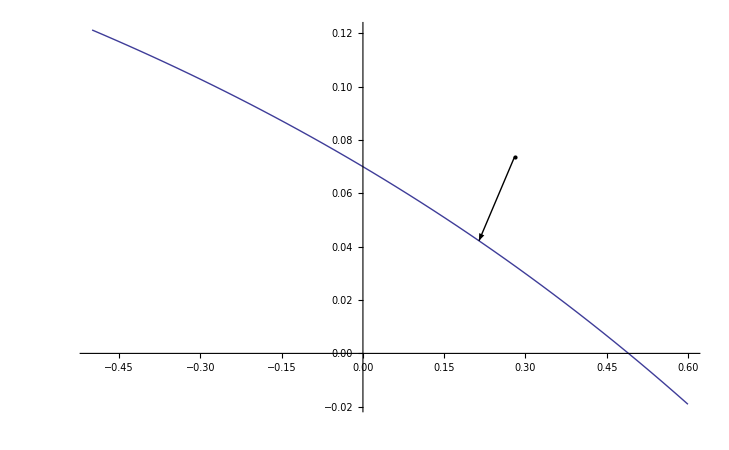

```mathematica
pt={0.01,0.15,0.12};
I1=pt[[1]]+pt[[2]]+pt[[3]]
sig1=pt[[1]];
sig2=pt[[2]];
solmin=MinF1[pt];
i1sqrtj2=UpdateF1[solmin]/.subst;
sig3=pt[[3]];
sqrtJ2=Sqrt[1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)];
point=Graphics[Point[{I1,sqrtJ2}]];
vec=Graphics[Arrow[{{I1,sqrtJ2},i1sqrtj2}]];
pl=Plot[FF[I1,0]/.subst,{I1,-0.5,0.6},AxesOrigin->{0,0},PlotRange->All];
Show[pl,point,vec]
```

```mathematica
gerenciamento das funcoes implementadas
```

das funcoes gerenciamento implementadas

```mathematica
ProjectSandlerExtPV[E_,EP_,k_]:=Block[{sqrtJ2,sig1,sig2,sig3,newsig,sqrtdeltaJ2,spc,stress,pt,xirhobeta,yield,I1,ksol,EPnext,Enext,sol,sigsol,deltaI1,deltaS,deltasig,K,G,I1proj,I1sqrtj2,delnewsig},
stress=Sigma[E-EP];
(*spc=Spectrum[stress];*)
spc=Eigenvalues[stress];
(*Print["spc = ",spc];*)
pt={spc[[1]],spc[[2]],spc[[3]]};
(*Print["ktrial = ",k];
Print["sigtrial = ",pt];
Print["yieldtrial = ",YieldFunction[pt,k]];*)
yield=YieldFunction[pt,k];
I1=pt[[1]]+pt[[2]]+pt[[3]];
(*Print["I1trial = ",I1];*)
If[(yield[[2]]≤0 && I1≤k)||(yield[[1]]≤0 && I1>k),
EPnext=EP;
ksol=k;
sigsol=pt;
newsig=stress;
Print["Elastic"];
,

If[(yield[[2]]>0 && I1<k),

(*Print["F2"];*)
sol=MinF2[pt,k];
sol[[3]]+=k;
sigsol=UpdateF2Principal[sol]/.subst;
ksol=sol[[3]];
,
	Print["F1"];
	sol=MinF1[pt];
	sigsol=UpdateF1Principal[sol]/.subst;
	I1proj=sigsol[[1]]+sigsol[[2]]+sigsol[[3]];
	ksol=MinResL[pt,k,I1,I1proj];
	If[ksol>I1proj,
		Print["Ring"];
		sol=MinF2θconst[pt,ksol];
		sol[[3]]+=k;
		sigsol=UpdateF2Principal[sol]/.subst;
		ksol=sol[[3]];
	];

];
(*Print["Plastic"];*)
I1sqrtj2=FromSigToI1SqrtJ2[sigsol];
newsig=CalcNewSig[stress,I1sqrtj2];
delnewsig=stress-newsig;
EPnext=EP+ComputeStrain[delnewsig]/.subst;

];

(*Print["ksol = ",ksol];
Print["sigsol = ",sigsol];
Print["yield = ",YieldFunction[sigsol,ksol]];*)
Return[{newsig,EPnext,ksol}]
];
```

Elastic

F1

F1

F1

«8 more identical outputs»

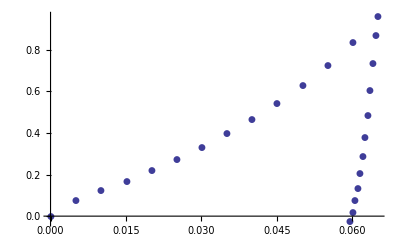

```mathematica
dEps={{-0.005,0,0},{0,0,0},{0,0,0}};
Eps={{-0.0000001,0,0},{0,0,0},{0,0,0}};
EP={{0,0,0},{0,0,0},{0,0,0}};
k=0.13;
solu={};
solu2={};
sigg={{0,0,0},{0,0,0},{0,0,0}};
For[i=1,i≤25,i++,
(*Print[" i = ",i];*)
soll=ProjectSandlerExtPV[Eps,EP,k];
(*Print[ "soll = ",soll];*)
{sigg,EP,k}=soll;
AppendTo[solu,{-Eps[[1,1]],-sigg[[1,1]]}];
AppendTo[solu2,{Tr[sigg],Sqrt[j2[sigg]]}];
If[i==14,dEps=-0.0005;dEps*=-1];
Eps+=dEps;
];
ListPlot[solu,AxesOrigin->{0,0},PlotMarkers->Automatic,PlotRange->All]
```

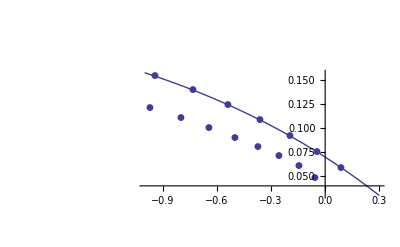

```mathematica
plt=Plot[FF[I11,0]/.subst,{I11,-1,0.3}];
lplt=ListPlot[solu2,AxesOrigin->{0,0},PlotMarkers->Automatic,PlotRange->All];
Show[plt,lplt]
```

```mathematica
Projecao sobre Func1
```

Func1 Projecao sobre

```mathematica
pt={0.01,0.13,0.1};
sigma=pt IdentityMatrix[3];
lprev=0.13;
sol=MinF1[pt]
UpdateF1[sol]
v1=Graphics3D[{Arrow[{pt,F1[sol[[1]],sol[[2]]]/.subst}]}];
sol1=FindRoot[{F1[ξ,β]-F2[θ,β,lprev]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]]
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]]

(*
f1pts=Table[(F1HWCart[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]+lprev,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f2pts=Table[(F2HWCart[θ,β,sol[[3]]+lprev]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph1=Graphics3D[Table[{Blue,Point[{f1pts[[i]]}]},{i,1,Length[f1pts]}]];
graph2=Graphics3D[Table[{Red,Point[{f2pts[[i]]}]},{i,1,Length[f2pts]}]];
Show[v1,graph1,graph2,PlotRange->All];
*)

f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,lprev,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,lprev]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Blue,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Black,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]
```

{0.116452,2.89903}

{0.201701,0.0439546}

0.122016

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.283077

-Graphics3D-

```mathematica
Projecao sobre Func2
```

Func2 Projecao sobre

```mathematica
pt={0.1,-0.56,-0.3};
sigma=pt IdentityMatrix[3];
(*JJJ2=1/2 Tr[s[sigma].s[sigma]]
ii1=Tr[sigma]*)
lprev=0.13;
(*NewtonFuncL[0.13,{ii1,Sqrt[JJJ2]}]*)
sol=MinF2[pt,lprev];
sol[[3]]+=lprev;
(*1/2(1+Sin[3 sol[[2]]]+1/ψ(1-Sin[3 sol[[2]]]))/.subst*)
UpdateF2Principal[sol];
v1=Graphics3D[{Arrow[{pt,F2[sol[[1]],sol[[2]],sol[[3]]]/.subst}]}];

sol1=FindRoot[{F1[ξ,β]-F2[θ,β,sol[[3]]]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]];
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]];


f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Blue,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Black,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics3D-

```mathematica
sig1v={1,1,1}/Sqrt[3]
(*sig2eq=alfa{1,0,0}+beta sig1v*)
sig2eq=alfa{1,0,0}+beta sig1v
sol1=Solve[{Norm[sig2eq]==1,sig1v.sig2eq==0},{alfa,beta}][[1]]
sig2v=sig2eq/.sol1
sig3v=Cross[sig1v,sig2v]
Rot={sig1v,sig2v,sig3v}
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
i1[sigma_]:=Tr[sigma]; 
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]];
sig={sig1,sig2,sig3}.IdentityMatrix[3];
rho=Sqrt[2]Sqrt[j2[sig]]
xi=Sqrt[3]i1[sig]

graph1sigs=Graphics3D[{Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}];
graph2cart=Graphics3D[{Arrow[{{0,0,0},sig1v}],Arrow[{{0,0,0},sig2v}],Arrow[{{0,0,0},sig3v}]}];
Show[graph1sigs,graph2cart]
```

{1/(√3),1/(√3),1/(√3)}

{0.6046+alfa,0.6046,0.6046}

Solve::ivar: 1.0472 is not a valid variable.

{√(0.731082+Abs[0.6046+alfa]^2)==1,0.698132+(0.6046+alfa)/(√3)==0}

ReplaceAll::reps: {√0.731082  + Abs[0.6046  + alfa]^2 == 1, 0.698132  + 0.6046  + alfa/√3 == 0}
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0.6046+alfa,0.6046,0.6046}/.{√(0.731082+Abs[0.6046+alfa]^2)==1,0.698132+(0.6046+alfa)/(√3)==0}

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{1/(√3),1/(√3),1/(√3)}×({0.6046+alfa,0.6046,0.6046}/.{√(0.731082+Abs[0.6046+alfa]^2)==1,0.698132+(0.6046+alfa)/(√3)==0})

{{1/(√3),1/(√3),1/(√3)},{0.6046+alfa,0.6046,0.6046}/.{√(0.731082+Abs[0.6046+alfa]^2)==1,0.698132+(0.6046+alfa)/(√3)==0},{1/(√3),1/(√3),1/(√3)}×({0.6046+alfa,0.6046,0.6046}/.{√(0.731082+Abs[0.6046+alfa]^2)==1,0.698132+(0.6046+alfa)/(√3)==0})}

0.228619

0.484974

-Graphics3D-

```mathematica
pt={0.1,-0.16,-0.1};
sigma=pt IdentityMatrix[3];
lprev=0.13;
sol=MinF2[pt,lprev];
sol[[3]]+=lprev;
UpdateF2Principal[sol];
v1=Graphics3D[{Arrow[{pt,F2[sol[[1]],sol[[2]],sol[[3]]]/.subst}]}];

sol1=FindRoot[{F1[ξ,β]-F2[θ,β,sol[[3]]]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]];
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]];
(*graph3=ParametricPlot3D[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2},{β,0,2Pi}, PlotStyle->{Opacity[0.2],Black,Frame->False}];
graph4=ParametricPlot3D[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi},{β,0,2Pi} ,PlotStyle->{Opacity[0.2],Black,Frame->False}];*)

f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Blue,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Blue,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics3D-

{0.0128547,-0.0564273,-0.0564273}

{0.121722,0.0091389,0.0091389}

{0.135295,0.0573526,0.0573526}

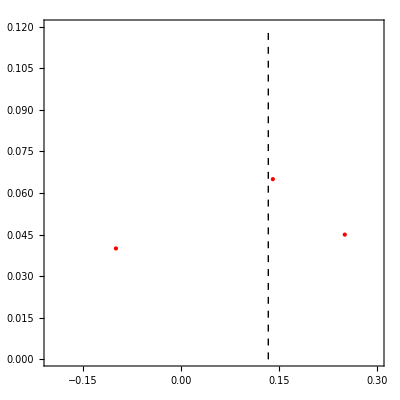

```mathematica
k0=0.13304482;
pt1={-0.1,0.04};
pt2={0.14,0.065};
pt3={0.25,0.045};
pt1sig=CalcNewSigFroI1J2Beta[{-0.1,0.04,0}]
pt2sig=CalcNewSigFroI1J2Beta[{0.14,0.065,0}]
pt3sig=CalcNewSigFroI1J2Beta[{0.25,0.045,0}]

b=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
c=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
d=Graphics[{PointSize[Large],Red,Point[pt1]}];
e=Graphics[{PointSize[Large],Red,Point[pt2]}];
f=Graphics[{PointSize[Large],Red,Point[pt3]}];

Show[b,c,d,e,f]
```

```mathematica
sol1=MinF2[pt1sig,k0];
sol1[[3]]=k0+sol1[[3]];

pt1sol=UpdateF2[sol1]
sol2=MinF2θconst[pt2sig,k0];
sol2[[3]]=k0+sol2[[3]];
pt2sol=UpdateF2[sol2]
sol3=MinF1[pt3sig];
pt3sol=UpdateF1[sol3]
```

{0.00826427,0.0287673}

resnorm = 0.000658843

resnorm = 1.3407×10^-7

resnorm = 3.78031×10^-14

resnorm = 5.55112×10^-17

{0.132251,0.0531279}

{0.237251,0.038988}

```mathematica
UpdateF2Principal[sol1]/.subst
UpdateF2Principal[sol2]/.subst
UpdateF1Principal[sol3]/.subst
```

{0.0359724,-0.0138541,-0.0138541}

{-0.017263,0.0747572,0.0747572}

{0.124103,0.0565738,0.0565738}

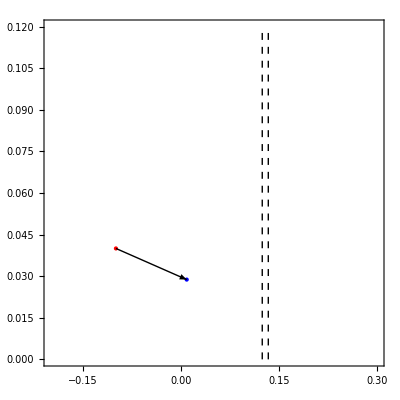

```mathematica
g=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Thick]}];
h=ContourPlot[{(elips[I1,sqrtJ2,sol1[[3]]]/.subst)==0,I1==sol1[[3]]},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
ii=Graphics[{PointSize[Large],Blue,Point[pt1sol]}];
arrow=Graphics[Arrow[{pt1,pt1sol}]];
Show[b,c,d,g,h,ii,arrow]
```

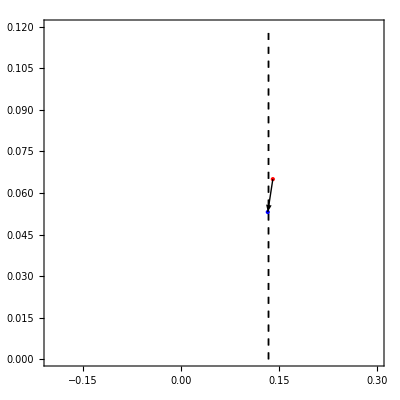

```mathematica
j=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Thick]}];
l=ContourPlot[{(elips[I1,sqrtJ2,sol2[[3]]]/.subst)==0,I1==sol2[[3]]},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
m=Graphics[{PointSize[Large],Blue,Point[pt2sol]}];
arrow=Graphics[Arrow[{pt2,pt2sol}]];
Show[b,c,e,j,l,m,arrow]
```

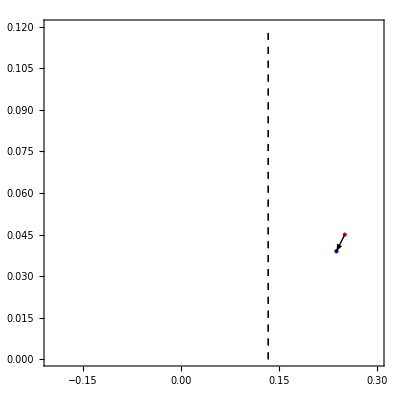

```mathematica
n=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Thick]}];
o=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
p=Graphics[{PointSize[Large],Blue,Point[pt3sol]}];
arrow=Graphics[Arrow[{pt3,pt3sol}]];
Show[b,c,f,n,o,p,arrow]
```

```mathematica
Young=29269.;
Poisson=0.203;
Young/(2(1+Poisson))
```

12165.

```mathematica
Sqrt[2125.]
```

46.0977

A constante da Efeito

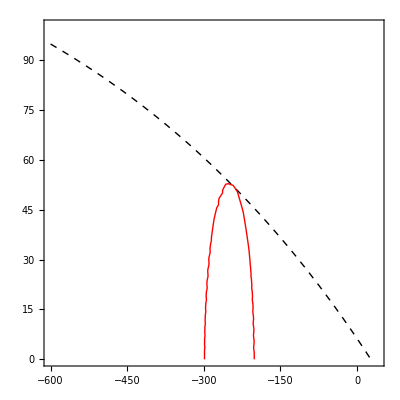

```mathematica
Efeito da constante A
FF[x_]:=A-C Exp[x B];
elips[I1_,SqrtJ2_,k_]:=((I1-k)/(R FF[k]))^2+(SqrtJ2/FF[k])^2-1
k0=-250.;
sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424,ψ->1,NN->0,G->12165};
aef=ContourPlot[{(sqrtJ2-FF[I1]/.sub)==0},{I1,-600,40},{sqrtJ2,0,100},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
bef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.sub)==0},{I1,-600,40},{sqrtJ2,0,100},ContourStyle->{Directive[Red,Thick]}];
Show[aef,bef]
```

B constante da Efeito

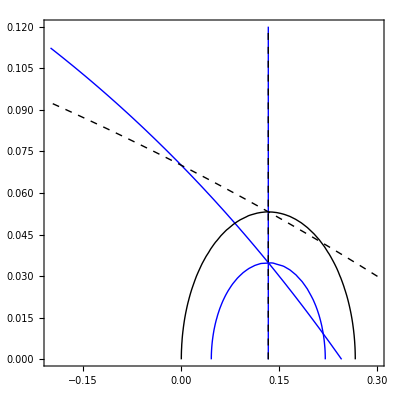

```mathematica
Efeito da constante B
sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424,ψ->1,NN->0,G->40};
aef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
bef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
subst = {D->  0.67,R->2.5(*5.3307429045*),A->  0.25,B->  2*0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
Daef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Dbef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Show[Daef,Dbef,aef,bef]
```

C constante da Efeito

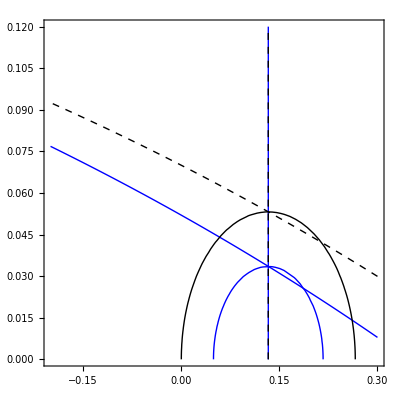

```mathematica
Efeito da constante C 
sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424,ψ->1,NN->0,G->40};
aef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
bef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
subst = {D->  0.67,R->2.5(*5.3307429045*),A->  0.25,B->  0.67,C->1.1* 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
Daef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Dbef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Show[Daef,Dbef,aef,bef]
```

constante da Efeito R

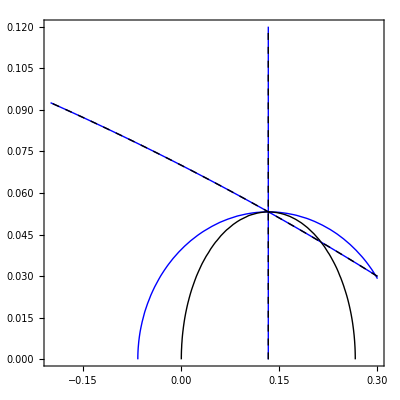

```mathematica
Efeito da constante R 
sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424,ψ->1,NN->0,G->40}
aef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
bef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Black,Directive[Black,Dashed,Thick]}];
subst = {D->  0.67,R->1.5*2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
Daef=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Dbef=ContourPlot[{(elips[I1,sqrtJ2,k0]/.subst)==0,I1==k0},{I1,-0.2,0.3},{sqrtJ2,0,0.12},ContourStyle->{Blue}];
Show[Daef,Dbef,aef,bef]
```

```mathematica
FF[x_]:=(fA-fC Exp[x fB]);
EpsEqX[X_]:=fW (E^(fD X))(*phil mexeu *)
XEqL[L_]:=L-fR FF[L]
EpsEqL[L_]:=EpsEqX[XEqL[L]]

sub={A->152.54,B->0.0015489,C->146.29,D->0.018768,W->0.006605,R->0.91969,K->16424}
```

{A→152.54,B→0.0015489,C→146.29,D→0.018768,W→0.006605,R→0.91969,K→16424}

```mathematica
FindRoot[eq1,{L,0}]
```

FindRoot::nlnum: The function value {eq1} is not a list of numbers with dimensions {1} at {L} = {0.}.

FindRoot[eq1,{L,0}]

```mathematica
FullSimplify[D[EpsEqL[L],L]]//CForm
```

Power(E,fD*(-(fA*fR) + Power(E,fB*L)*fC*fR + L))*fD*(1 + Power(E,fB*L)*fB*fC*fR)*fW

```mathematica
FullSimplify[D[EpsEqL[L],L]]
```

ⅇ^(fD (-fA fR+ⅇ^(fB L) fC fR+L)) fD (1+ⅇ^(fB L) fB fC fR) fW

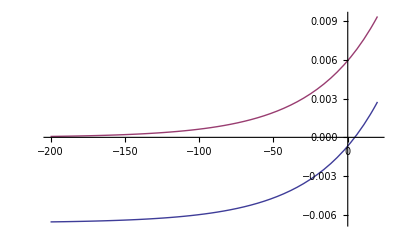

```mathematica
eq1=0.006605 (-1+ⅇ^(0.018768 (-0.91969 (152.54-146.29 ⅇ^(0.0015489 L))+L)));
eq2=0.006605 ⅇ^(0.018768 (-0.91969 (152.54-146.29 ⅇ^(0.0015489 L))+L));
Plot[{eq1,eq2},{L,-200,20},AxesOrigin->{0,0}]
```

```mathematica
ResL[pt_,θ_,β_,L_,Lprev_]:=Block[{resl,haigh,haightrial,G,K,Rot,depspdl,A,R,B,W,d,I1,I1tr,ϕ,δL,l,L0,delepsp},

I1tr=pt[[1]]+pt[[2]]+pt[[3]];
I1=R FF[L]Cos[θ]+L;
delepsp=EpsEqL[L]-EpsEqL[Lprev];
resl=3K delepsp- (I1tr-I1);
Return[resl]
];
ff=Table[Simplify[ResL[{sig11,sig22,sig33},θ,β,L,4.75376]/.sub]/.{sig11->-45.9,sig22->-62.1,sig33->-48.2},{θ,Pi/2,Pi,Pi/20}];
Plot[ff,{L,-50,10}]
```

-Graphics-

```mathematica
Pi/4 180/Pi
```

45

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

{-1/(√2),1/(√2)}

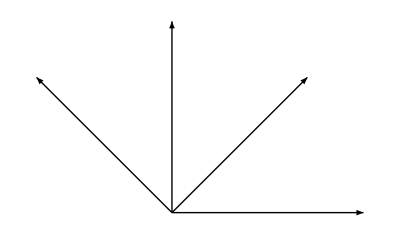

{{c1→1/(√2),c2→-1/(√2)},{c1→-1/(√2),c2→1/(√2)}}

-Graphics-

```mathematica
v={1/Sqrt[2],1/Sqrt[2]};
u={1,0};
uu={0,1};
c={c1,c2};
rot[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
rot[Pi/4]//MatrixForm
cs=rot[Pi/4+Pi/2].u
Graphics[{Arrow[{{0,0},cs}], Arrow[{{0,0},v}], Arrow[{{0,0},u}], Arrow[{{0,0},uu}]}]
Solve[{v.c==0,Norm[c]==1},{c1,c2}]
cs={-1/Sqrt[2],1/Sqrt[2]};
Graphics[{Arrow[{{0,0},cs}], Arrow[{{0,0},v}], Arrow[{{0,0},u}], Arrow[{{0,0},uu}]}]
```

```mathematica
ArcCos[1/Sqrt[3]]
```

ArcCos[1/(√3)]

```mathematica
rot3D[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
rot3D2[θ_]:={{Cos[θ],0,-Sin[θ]},{0,1,0},{Cos[θ],0,Sin[θ]}};
rot3D3[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}};
rot3D[θ]//MatrixForm
rot3D2[θ]//MatrixForm
rot3D3[θ]//MatrixForm
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
Transpose[rot3D[θ]].rot3D[θ]//MatrixForm
r=rot3D[-ArcCos[1/(√3)]];
r2=rot3D2[-ArcCos[1/(√3)]];
r3=rot3D3[-ArcCos[1/(√3)]];
v1={1,0,0};
v2={0,1,0};
v3={0,0,1};
vxi=1/Sqrt[3]{1,1,1};
v={vx,vy,vz};
w={w1,w2,w3};
Solve[{vxi.v==0,Norm[v]==1,Norm[w]==1,Cross[v,w]==vxi},{vx,vy,vz,wx,wy,wz}]
v0={0,0,0};
vxi2=rot3D[Pi/2].vxi
Graphics3D[{Arrow[{v0,v1}],Arrow[{v0,v2}],Arrow[{v0,v3}],Arrow[{v0,vxi}],Arrow[{v0,vxi2}]}]
```

(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

(Cos[θ] | 0 | -Sin[θ]
0 | 1 | 0
Cos[θ] | 0 | Sin[θ])

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

(Cos[θ]^2+Sin[θ]^2 | 0 | 0
0 | Cos[θ]^2+Sin[θ]^2 | 0
0 | 0 | 1)

{}

{-1/(√3),1/(√3),1/(√3)}

-Graphics3D-

```mathematica
Simplify[r3.(r2.(r.v1))]
```

{1/3,1/9 √2 (-3+√3),1/9 (6+√3)}

```mathematica
vxi=1/Sqrt[3]{1,1,1};
v={vx,vy,vz};
w={wx,wy,wz};
Simplify[Solve[{vxi.v==0,Cross[v,w]==vxi,v.w==0,w.vxi==0},{vx,vy,vz,wx,wy,wz}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{vx→-vy-vz,wx→(-vy+vz)/(2 √3 (vy^2+vy vz+vz^2)),wy→-(vy+2 vz)/(2 √3 (vy^2+vy vz+vz^2)),wz→(2 vy+vz)/(2 √3 (vy^2+vy vz+vz^2))},{vx→-vz,vy→0,wx→1/(2 √3 vz),wy→-1/(√3 vz),wz→1/(2 √3 vz)}}

```mathematica
A={a1,a2,a3};
B={b1,b2,b3};
Cc={1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
eqs={Cross[B,A]==Cc,A.B==0,B.Cc==0,Cc.A==0}
FullSimplify[Solve[eqs,{a1,a2,a3,b1,b2,b3}]]
x=1/Sqrt[2];
A={0,a2,-a2}/.{a2->x}
B={1/(Sqrt[3]a2),-1/(2Sqrt[3]a2),-1/(2Sqrt[3]a2)}/.{a2->x}
Graphics3D[{Arrow[{{0,0,0},A}],Arrow[{{0,0,0},B}],Arrow[{{0,0,0},Cc}]}]
```

{{a3 b2-a2 b3,-a3 b1+a1 b3,a2 b1-a1 b2}=={1/(√3),1/(√3),1/(√3)},a1 b1+a2 b2+a3 b3==0,b1/(√3)+b2/(√3)+b3/(√3)==0,a1/(√3)+a2/(√3)+a3/(√3)==0}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a3→-a1-a2,b1→(a1+2 a2)/(2 √3 (a1^2+a1 a2+a2^2)),b2→-(2 a1+a2)/(2 √3 (a1^2+a1 a2+a2^2)),b3→(a1-a2)/(2 √3 (a1^2+a1 a2+a2^2))},{a1→0,a3→-a2,b1→1/(√3 a2),b2→-1/(2 √3 a2),b3→-1/(2 √3 a2)}}

{0,1/(√2),-1/(√2)}

{√(2/3),-1/(√6),-1/(√6)}

-Graphics3D-

```mathematica
Integrate[m vv[t],t]
```

m ∫vv[t]ⅆt